# Zestaw 2

## Zadanie 1. Rozwiązywanie równań, Solve, Plot, Epilog

#### Rozwiąż równanie:

```mathematica
f[x_] := x^3 + x^2 -4x - 4
```

```mathematica
?Solve
```

```mathematica
solutions = Solve[f[x] == 0, x]
```

{{x→-2},{x→-1},{x→2}}

#### Wyrysuj funkcję używając polecania Plot w zakresie

```mathematica
?Plot
```

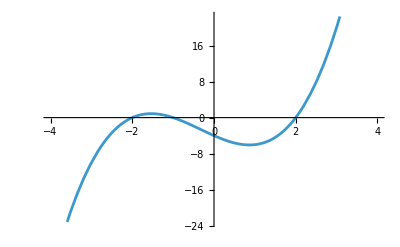

```mathematica
Plot[f[x], {x, -4, 4}]
```

#### Na wykresie zaznacz rozwiązania równania, w formie czerwonych punktów. Podpisz osie wykresu

```mathematica
GetSolutionPoints[f_, solutions_] := Map[
x |-> {x, f[x]},
Values[Flatten[solutions]]
]
```

```mathematica
solutionPoints = GetSolutionPoints[f, solutions]
```

{{-2,0},{-1,0},{2,0}}

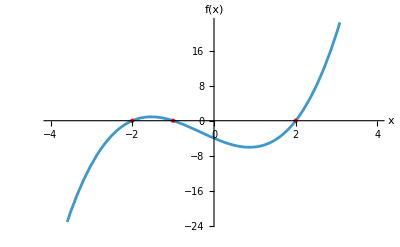

```mathematica
Plot[
f[x], {x,-4,4},
Epilog->{Red, PointSize[Large], Point[solutionPoints]},
AxesLabel->{"x","f(x)"}
]
```

## Zadanie 2. Rozwiązywanie równań, liczba rozwiązań, Solve, Plot, Reduce, Epilog, Manipulate

Zdefiniuj funkcje  (jak w poprzednim zadaniu) oraz , 
gdzie 𝑎 jest parametrem rzeczywistym.

```mathematica
f[x_] := x^3 + x^2 -4x - 4
```

```mathematica
g[a_, x_] := x^2 + a
```

Rozwiąż równanie:

```mathematica
Solve[f[x] == g[a, x], x, Reals]
```

{{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,1], ]},{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,2], ]},{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,3], ]}}

### 1) Dla 𝑎 = 0, podaj rozwiązania (1) w ℝ (zbiór liczb rzeczywistych)

```mathematica
a=0;
solutions = Solve[f[x] == g[a, x], x, Reals]
```

{{x→}}

Przedstaw funkcje 𝑓(𝑥) oraz 𝑔(𝑥) na wykresie

```mathematica
PlotFunctions[a_, aStr_, solutions_] := Plot[
{f[x], g[a, x]},
{x,-3,3},
Epilog->{PointSize[Large], Red, Point[GetSolutionPoints[f, solutions]]},
PlotLegends->{"y = f(x)", "y = g(" <> aStr <> ", x)"},
AxesLabel->{"x", "y"}
];
```

```mathematica
PlotFunctions[a_, solutions_] := PlotFunctions[a, ToString[a], solutions]
```

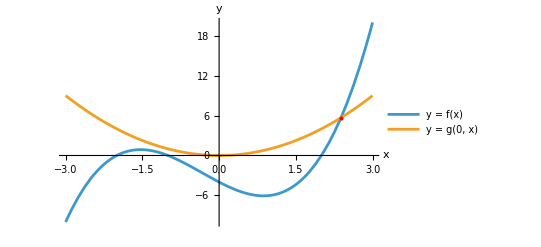

```mathematica
PlotFunctions[a, solutions]
```

Ile jest punktów przecięcia obu funkcji?

```mathematica
Length[Flatten[solutions]]
```

1

### 2) Dla , podaj rozwiązania (1) w ℝ

```mathematica
a = -1;
solutions = Solve[f[x] == g[a, x], x, Reals]
```

{{x→-1},{x→1/2 (1-√13)},{x→1/2 (1+√13)}}

Przedstaw graficznie rozwiązania równania

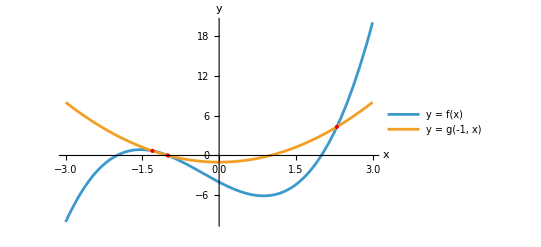

```mathematica
PlotFunctions[a, solutions]
```

### 3) Dla dowolnego 𝑎, określ przedziały 𝑎, dla których równanie (1) ma określoną liczbę rozwiązań

Przedstaw graficznie każdą sytuację, w której przy zmianie wartości 𝑎 zmienia się liczba rozwiązań, skorzystaj z Plot.
Rozwiązania (1) przedstaw na wykresie  w formie czerwonych punktów.

Wskazówka: W punkcie 3) wydostań warunki na obecność danego rozwiązania używając funkcji Part. Te warunki  to  nierówności  na  𝑎.
Używając  funkcji  Reduce należy  je  rozwiązać. Można  użyć funkcji FullSimplify by uprościć wyrażenia.

```mathematica
Clear[a];
solutionsForA = Solve[f[x] == g[a, x], x, Reals]
```

{{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,1], ]},{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,2], ]},{x→ConditionalExpression[Root[-4-a-4 #1+#1^3&,3], ]}}

```mathematica
ExtractCondition[expression_] := FirstCase[
expression, 
ConditionalExpression[_,c_]:>c,
Missing[],{0,-1}
]
```

```mathematica
inequalities = Map[e |-> ExtractCondition[e[[1]]], solutionsForA]
```

{4/9 (-9-4 √3)<a<4/9 (-9+4 √3)||a>4/9 (-9+4 √3)||a<4/9 (-9-4 √3),4/9 (-9-4 √3)<a<4/9 (-9+4 √3),4/9 (-9-4 √3)<a<4/9 (-9+4 √3)}

```mathematica
?Reduce
```

#### 3 rozwiązania

```mathematica
threeSolutions = FullSimplify[Reduce[inequalities, {a}]]
```

-4/9 (9+4 √3)<a<4/9 (-9+4 √3)

```mathematica
SolveAndPlot[a_, aStr_] := Module[
{solutions},
solutions = Solve[f[x] == g[a, x], {x}, Reals];
PlotFunctions[a, aStr, solutions]
];
SolveAndPlot[a_] := SolveAndPlot[a, ToString[a]]
```

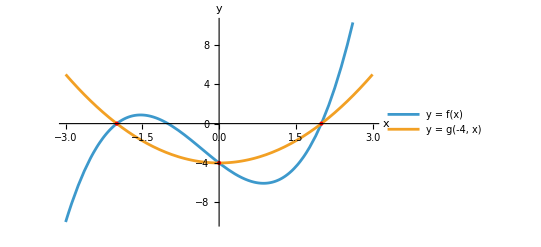

```mathematica
SolveAndPlot[-4]
```

#### 2 rozwiązania

Zauważmy, że:

```mathematica
inequalities[[2]] === inequalities[[3]]
```

True

```mathematica
Reduce[{
Not[inequalities[[1]]],
inequalities[[2]]
}]
```

False

```mathematica
noSolutions = FullSimplify[Reduce[{
Not[inequalities[[1]]],
Not[inequalities[[2]]]
}]]
```

36+16 √3+9 a==0||9 (4+a)==16 √3

```mathematica
{a1, a2} = Values[Flatten[Solve[noSolutions]]]
```

{-4/9 (9+4 √3),4/9 (-9+4 √3)}

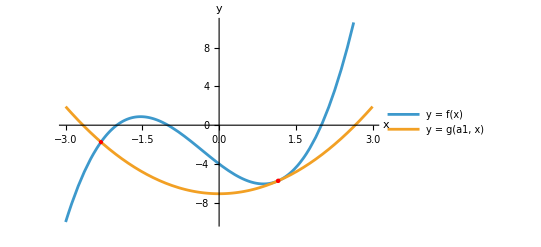

```mathematica
SolveAndPlot[a1, "a1"]
```

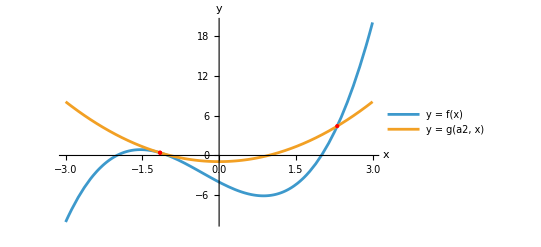

```mathematica
SolveAndPlot[a2, "a2"]
```

#### 1 rozwiązanie

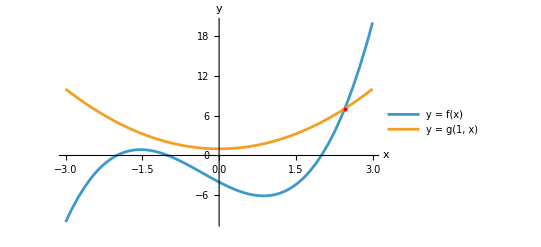

```mathematica
SolveAndPlot[1]
```

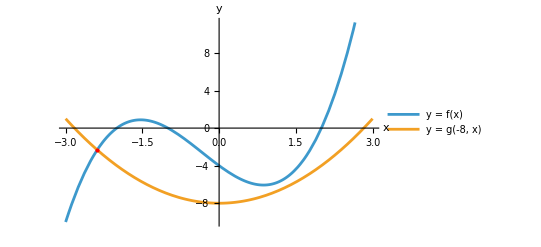

```mathematica
SolveAndPlot[-8]
```

#### 4) Skorzystaj z funkcji Manipulate, by przedstawić wykres z 3)

Zakres 𝑎 zdefiniuj od -10 do 5.

```mathematica
?Manipulate
```

```mathematica
Manipulate[SolveAndPlot[a], {a, -10, 5}]
```

## Zadanie 3. Rozwiązywanie równań, dziedzina rozwiązań, Solve

Sprawdź jakie są rozwiązania równania  przy użyciu funkcji Solve:

```mathematica
p[x_] := a x^2 + b x + c
```

### 1) bez specyfikacji dziedziny

```mathematica
Solve[p[x] == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Jaka jest domyślna dziedzina dla równań w funkcji Solve?

Odp: Liczby zespolone

### 2) z dziedziną w zbiorze liczb rzeczywistych, ℝ

```mathematica
Solve[p[x] == 0, x, Reals]
```

{{x→ConditionalExpression[-b/(2 a)-1/2 √((b^2-4 a c)/a^2), ]},{x→ConditionalExpression[-b/(2 a)+1/2 √((b^2-4 a c)/a^2), ]}}

### To samo sprawdź dla równia

```mathematica
p[x_] := a x^3 + b x^2 + c x+ d
```

```mathematica
Solve[p[x] == 0, x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
Solve[p[x] == 0, x, Reals]
```

{{x→ConditionalExpression[Root[d+c #1+b #1^2+a #1^3&,1], ]},{x→ConditionalExpression[Root[d+c #1+b #1^2+a #1^3&,2], ]},{x→ConditionalExpression[Root[d+c #1+b #1^2+a #1^3&,3], ]}}

### Rozważ równanie dla wielomianu 𝑛-tego stopnia

Rozważ równanie dla wielomianu 𝑛-tego stopnia postaci .
Dla jakich wartości 𝑛 istnieją ogólne wzory na rozwiązanie tego równania? Sprawdź w Mathematica® dla kilku
wybranych wartości 𝑛.

```mathematica
IndexToLetter[index_] := FromCharacterCode[First[ToCharacterCode["a"]]+ index]
```

```mathematica
Polynomial[n_] := Total[Map[k |->IndexToLetter[k] * x^(n - k), Range[0, n]]]
```

```mathematica
Polynomial[7]
```

h+g x+f x^2+e x^3+d x^4+c x^5+b x^6+a x^7

```mathematica
Solve[Polynomial[2] == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[Polynomial[4] == 0, x]
```

```mathematica
Solve[Polynomial[5] == 0, x]
```

{{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,1]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,2]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,3]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,4]},{x→Root[f+e #1+d #1^2+c #1^3+b #1^4+a #1^5&,5]}}

```mathematica
Solve[Polynomial[6] == 0, x]
```

{{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,1]},{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,2]},{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,3]},{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,4]},{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,5]},{x→Root[g+f #1+e #1^2+d #1^3+c #1^4+b #1^5+a #1^6&,6]}}

Ciekawostka: Na powyższe pytanie odpowiada Twierdzenie Abela-Ruffiniego

## Zadanie 4. Rozwiązywanie równań, wielomiany wyższych stopni, Product, Expand, Table, oraz inne

Utworzyć wielomian 10-stopnia, , o miejscach zerowych 𝑥1, 𝑥2, … , 𝑥𝑛 ∈ ℝ wylosowanych z rozkładu jednorodnego na przedziale [−1, 1].
W tym celu wylosuj miejsca zerowe korzystając z funkcji RandomReal, a następnie skorzystaj z funkcji Product by utworzyć wielomian ℎ(𝑥) o zadanych miejscach zerowych.

```mathematica
?RandomReal
```

```mathematica
roots = RandomReal[{-1, 1}, 10]
```

{0.0678822,0.232231,-0.512611,0.768357,-0.492279,-0.877876,0.281027,-0.446885,-0.532166,-0.0804542}

```mathematica
h[x_] := Product[x - roots[[i]], {i, Length[roots]}]
```

Następnie należy:

### 1) Wypisać wielomian korzystając z polecenia Expand[ℎ(𝑥)]

```mathematica
Expand[h[x]]
```

0.0000144282-0.0000321714 x-0.00300971 x^2+0.0001818 x^3+0.0705109 x^4+0.0859219 x^5-0.473687 x^6-1.08451 x^7+0.0219418 x^8+1.59277 x^9+x^10

### 2) Sprawdzić ile rozwiązań będzie miało równanie ℎ(𝑥) = 𝑎

gdzie 𝑎 jest parametrem zmieniającym się w wąskim zakresie od −0.01 do 0.01, co 0.0005.

```mathematica
aValues = Range[-0.01, 0.01, 0.0005]
```

{-0.01,-0.0095,-0.009,-0.0085,-0.008,-0.0075,-0.007,-0.0065,-0.006,-0.0055,-0.005,-0.0045,-0.004,-0.0035,-0.003,-0.0025,-0.002,-0.0015,-0.001,-0.0005,0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01}

Wyniki zachować jako lista nSol. Można użyć funkcji Table do zapełniania listy nSol.

```mathematica
nSol = Map[
a |-> {a, Length[Solve[h[x] == a, {x}, Reals]]},
aValues
]
```

{{-0.01,2},{-0.0095,2},{-0.009,2},{-0.0085,2},{-0.008,2},{-0.0075,2},{-0.007,2},{-0.0065,2},{-0.006,2},{-0.0055,2},{-0.005,2},{-0.0045,2},{-0.004,2},{-0.0035,2},{-0.003,2},{-0.0025,2},{-0.002,2},{-0.0015,2},{-0.001,2},{-0.0005,4},{0.,10},{0.0005,2},{0.001,2},{0.0015,2},{0.002,2},{0.0025,2},{0.003,2},{0.0035,2},{0.004,2},{0.0045,2},{0.005,2},{0.0055,2},{0.006,2},{0.0065,2},{0.007,2},{0.0075,2},{0.008,2},{0.0085,2},{0.009,2},{0.0095,2},{0.01,2}}

### 3) Przedstawić wartości nSol na wykresie korzystając z ListPlot

Upewnić się, że zakres wykresu obejmuje wszystkie punkty.
Zadbać o prezentację wyniku, zapoznać się z opcjami ListPlot przez F1 albo Options[ListPlot].

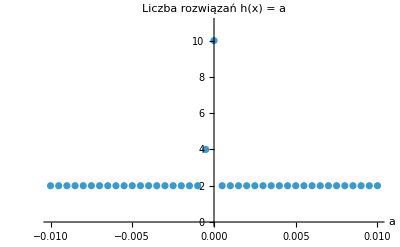

```mathematica
ListPlot[
nSol,
PlotRange->{0, Length[roots] + 1},
AxesLabel->{"a", "Liczba rozwiązań h(x) = a"}
]
```

### 4) Zautomatyzować proces generowania wykresu

Zautomatyzować proces generowania wykresu z punktu 3) tak by można było go otrzymać dla wielomianu ℎ(𝑥) z nowo wylosowanymi miejscami zerowymi.

```mathematica
GeneratePolynomialAndPlot[] := Module[
{},
roots = RandomReal[{-1, 1}, 10];
h[x_] := Product[x - roots[[i]], {i, Length[roots]}];
aValues = Range[-0.01, 0.01, 0.0005];
nSol = Map[
a |-> {a, Length[Solve[h[x] == a, {x}, Reals]]},
aValues
];
ListPlot[
nSol,
PlotRange->{0, Length[roots] + 1},
AxesLabel->{"a", "Liczba rozwiązań h(x) = a"}
]
];
```

Następnie utworzyć listę pSol zawierającą wykresy jak w punkcie 3) dla 9-ciu  różnych wielomianów ℎ(𝑥)  z wylosowanymi miejscami zerowymi.

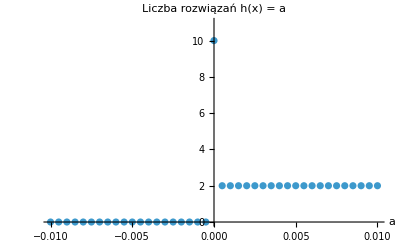
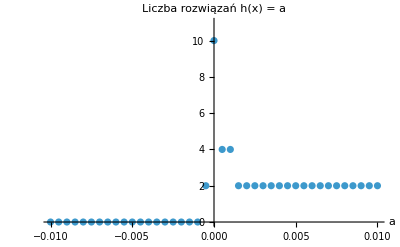
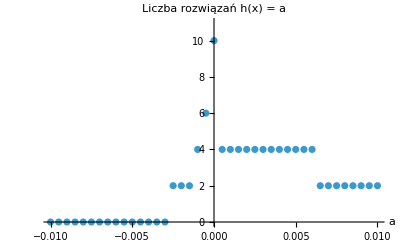
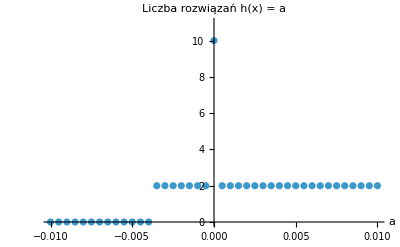
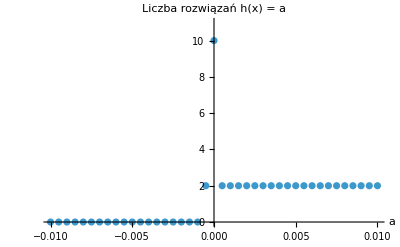
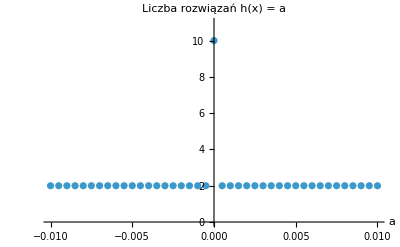
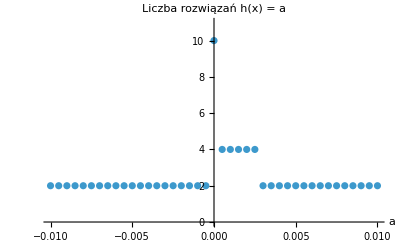
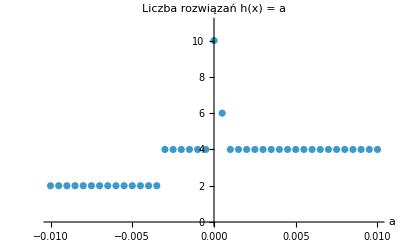

```mathematica
pSol = Map[plot |-> GeneratePolynomialAndPlot[], Range[9]]
```

### 5) Zadbać o prezentację wyniku z punktu 4)

Zapoznać się z funkcją Partition,  TableForm, GraphicsGrid.

```mathematica
?Partition
```

```mathematica
?TableForm
```

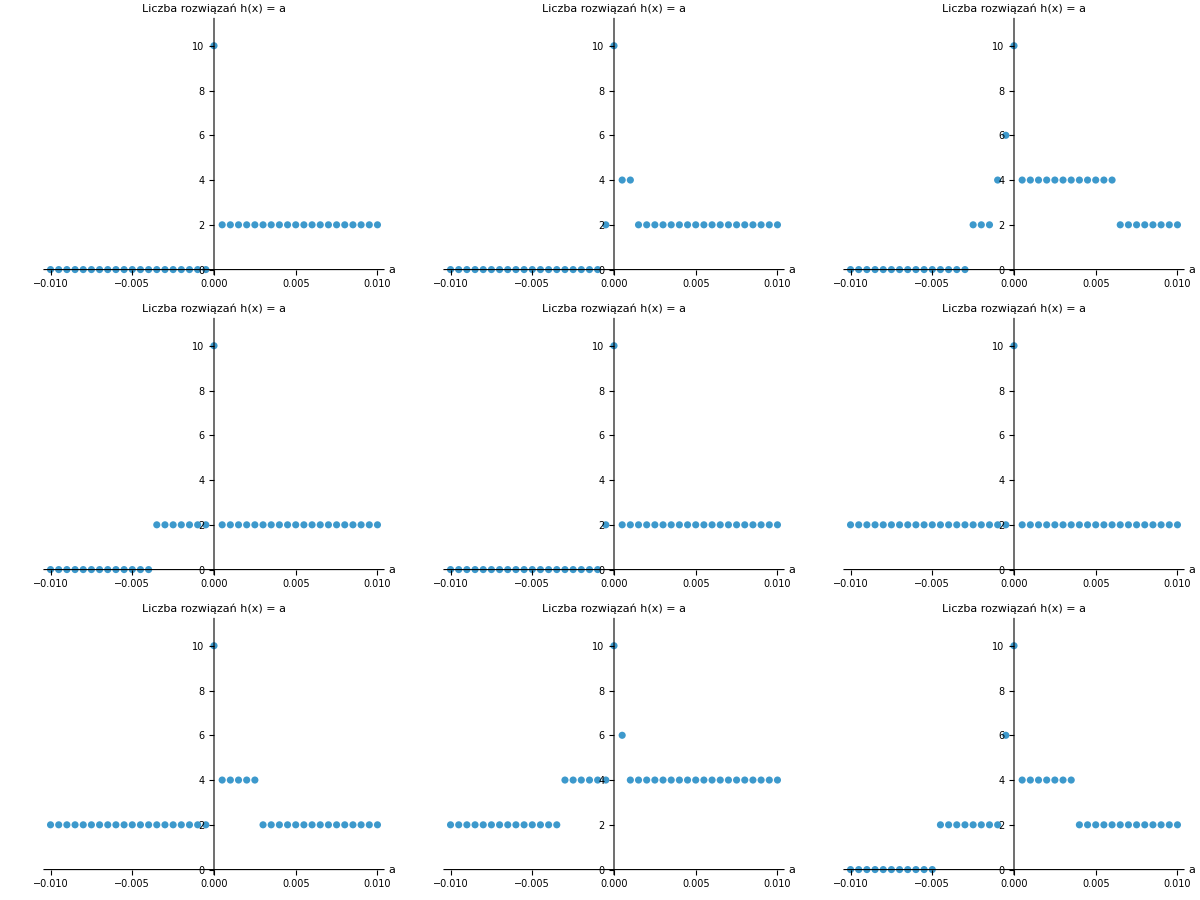

```mathematica
partitioned = Partition[pSol, 3];
TableForm[partitioned]
```

## Zadanie 5. Równania transcendentne, Solve, NSolve, FindRoot

Znaleźć rozwiązania równania: 3 sin(7x) - 2 ln(x) = 0

```mathematica
d[x_] := 3Sin[7x] - 2Log[x]
```

Korzystając z:

### 1) funkcji Solve z wybranym zakresem 𝑥

#### Wskazówka: By wybrać odpowiedni zakres narysuj na wykresie funkcje 3 sin(7𝑥) oraz 2 ln 𝑥.

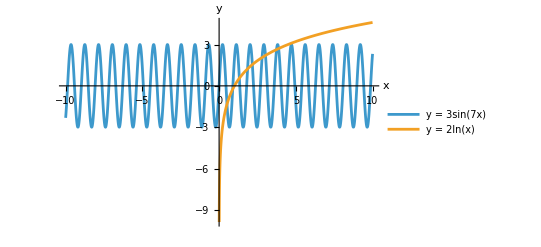

```mathematica
Plot[
{3 Sin[7x], 2 Log[x]},
{x, -10, 10},
PlotLegends->{"y = 3sin(7x)", "y = 2ln(x)"},
AxesLabel->{"x", "y"}
]
```

```mathematica
Solve[{d[x] == 0, 1/4 <= x <= 5}, Reals]
```

{{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

#### Co zwraca Solve, bez wybranego zakresu?

Jaki komunikat zwraca Mathematica®?

```mathematica
Solve[d[x] == 0, Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[-2 Log[x]+3 Sin[7 x]==0,ℝ]

### 2) NSolve

```mathematica
?NSolve
```

```mathematica
nSolveResult = NSolve[d[x] == 0, Reals]
```

{{x→0.514391},{x→0.886065},{x→1.31982},{x→1.8559},{x→2.16663},{x→2.80091},{x→3.02311},{x→3.74412},{x→3.87805}}

Ile rozwiązań zwraca ta funkcja?

```mathematica
Length[nSolveResult]
```

9

### 3) FindRoot

```mathematica
?FindRoot
```

```mathematica
findRootResult = FindRoot[d[x], {x, 1}]
```

{x→0.886065}

Ile rozwiązań zwraca ta funkcja?

```mathematica
Length[findRootResult]
```

1